```mathematica
Dimensionamento do revestimento de superfície
```

de Dimensionamento do revestimento superfície

## Preliminares

Conversão de unidades

```mathematica
<<Units`
Convert[1 Pound/Gallon,1 Kilogram/Meter^3]
Convert[1. Feet/Second^2,1 Meter/Second^2]
Convert[1 Feet,1Inch]
Convert[1 Gallon,1Inch^3]
12/231.
```

(119.826 Kilogram)/Meter^3

(0.3048 Meter)/Second^2

12 Inch

231. Inch^3

0.0519481

Dado dois pontos cria equação da reta

```mathematica
LinearEq[input_]:=Block[{y,x,temp,temp2,temp3,pt1,pt2},
pt1=input[[1]];
pt2=input[[2]];
temp=(pt2[[2]]-pt1[[2]])/(pt2[[1]]-pt1[[1]])(x-pt1[[1]])+pt1[[2]];
(*temp2=temp/.x->pt1[[1]];
temp3=temp/.x->pt2[[1]];
y=Piecewise[{{pt1[[1]],temp2>0},{pt2[[1]],temp3<pt2[[2]]}},temp];*)
Return[temp]
]
```

Tabela de Tubos

```mathematica
(* 1 - Outside diameter(in) | 2 - Nominal weight(lb/ft) | 3 - Grade | 4 - Wall thickness (in) | 5 - Inside diameter (in) | 6 - Pipe collapse resistance (psi) | 7 - Body yield strength (1000 lbf) | 8 - Coupling type | 9 - Internal pressure resistance (psi) | 10 - Joint strength (1000 lbf) *)
```

```mathematica
PipesTable={
{20,       94,   K55,0.438,19.124,520,  1480,LTC,2110,955 },
{20,       133,K55,0.635,18.730,1500,2125,BTC,3036,2123},
{16,        65,   K55,0.375,15.250,630,  1012,STC,2260,625},
{16,        75,   K55,0.438,15.124,1020,1178,STC,2630,752},
{16,        84,   L80,0.495,15.010,1480,1929,BTC,4330,1861},
{16,        109, K55,0.656,14.688,2560,1739,BTC,3950,1895},
{13.375,98,  L80,0.719,11.937,5910,2800,BTC,7530,2286},
{13.375,85, P110,0.608,12.159,4690,2682,PTC,8750,2290},
{13.375,98, P110,0.719,11.937,7280,3145,PTC,10350,2800},
{9.625, 58.4,L80,0.595,8.435,7890,1350,BTC,8650,1396},
{9.625, 47,   P110,0.472,8.681,5310,1493,LTC,9449,1213},
{7,          38,V150,0.540,5.920,19240,1644,EXTL,18900,1430},
{7,          41,V150,0.590,5.820,22810,1782,PTC,20200,1052},
{7,          46,V150,0.670,5.660,25970,1999,PTC,25070,1344},
{7,          38,MW155,0.540,5.920,19700,1697,EXTL,20930,1592},
{7,          46,SOO140,0.670,5.660,24230,865,PTC,23400,1222},
{7,          46,SOO155,0.670,5.660,26830,2065,PTC,25910,1344}
};
```

```mathematica
Janela operacional do poço exercício modelo Rahman pag. 125
```

do exercício Janela modelo operacional poço Rahman pag.125

Pressão de ruptura (psi)

```mathematica
ComputeBurstPressureSurfaceCasing[L_,MudWeigthToFrac_,MudWeigthToKick_,GasGrad_]:=Block[{SF=0.5(*SafetyFactor*),PI(*InjectionPressure*),SHP(*SurfaceHolePressure*),BHP(*BottomHolePressure*)},
PI=0.052(MudWeigthToFrac+SF)L;
SHP=PI-GasGrad L;
BHP=PI-MudWeigthToKick L 0.052;
{SHP,BHP}
];
ComputeBurstPressureSurfaceCasing[5000,14.76,8.95,0.1]
```

{3467.6,1640.6}

```mathematica
Pressão de Colapso do revestimento na base da sapata (psi)
```

base Colapso da de do na Pressão psi revestimento sapata

```mathematica
ComputeColapsePressureSurfaceCasing[L_,MudWeigth_]:=Block[{CP},
CP=0.052MudWeigth L;
CP
];
ComputeColapsePressureSurfaceCasing[5000,9.5]
```

2470.

```mathematica
Coordenadas das retas de ruptura e colapso
```

colapso Coordenadas das de e retas ruptura

```mathematica
BurstCoords={{3467.6,0},{1640.6,-5000}};
ColapseCoords={{0,0},{2470,-5000}};
```

Cálculo dos comprimentos e escolha dos revestimentos

```mathematica
SelecPipe[BurstCoords_,ColapseCoords_,CaseOD_,CaseLength_]:=Block[{plot={},i,eq1,eq2,CSF=0.85,BSF=1.1,sz,PipeLengthColapse,PipeLengthBurst,PCR,PBR,tolerance=0.1,grade,coupling,weight,OD},

eq1=LinearEq[BurstCoords];
eq2=LinearEq[ColapseCoords];

sz=Length[PipesTable];
For[i=0,i≤sz,i++,

If[Abs[(CaseOD-PipesTable[[i]][[1]])]<tolerance,

PBR=PipesTable[[i]][[9]] ;
PCR=PipesTable[[i]][[6]] ;
PBR=PBR /BSF;
PCR=PCR /CSF;
If[PBR>BurstCoords[[1,1]],
PipeLengthBurst=BurstCoords[[1,1]];
,
PipeLengthBurst=eq1/.x->PBR;
];

If[PCR>ColapseCoords[[2,1]],
PipeLengthColapse=ColapseCoords[[2,1]];
,
PipeLengthColapse=eq2/.x->PCR;
];

OD=PipesTable[[i]][[1]];
grade=PipesTable[[i]][[3]];
weight=PipesTable[[i]][[2]];
coupling=PipesTable[[i]][[8]];
(*If[PipeLengthColapse>PipeLengthBurst,
delta=PipeLengthColapse-PipeLengthBurst;
interval1=PipeLengthBurst+delta;
interval2=CaseLength-interval1;
Print[" OD = ",OD,"|| grade = ",grade,"|| coupling = ",coupling," || weight = ",weight," || interval1 = ",interval1," || interval2 = ",interval2," || interval1+interval2 = ",interval1+interval2];
];
*)

Print[" PCR ",PCR];
Print[" ",grade," ",weight,"# ", " LBurst = ",PipeLengthBurst ," ft"];
Print[" ",grade," ",weight,"# ", " LColapse = ",PipeLengthColapse ," ft"];
AppendTo[plot,ContourPlot[{eq1==y,eq2==y,x==PBR,x==PCR,y==PipeLengthBurst,y==PipeLengthColapse},{x,0,CaseLength},{y,0,-CaseLength},PlotLabel->{"GRADE = ",grade", || WEIGHT = ",weight} ,ContourLabels->{True,Large},ContourStyle->{{Thick,Dashed},{Thick,Blue},{Thick,Dashed},{Thick,Blue},{Thick,Dashed},{Thick,Blue}}]];
];

];

plot

];
```

Part::partd: Part specification List ⟦ 1 ⟧ is longer than depth of object.

PCR 741.176

K55 65#  LBurst = -3867.14 ft

K55 65#  LColapse = -1500.36 ft

PCR 1200.

K55 75#  LBurst = -2946.61 ft

K55 75#  LColapse = -2429.15 ft

PCR 1741.18

L80 84#  LBurst = 3467.6 ft

L80 84#  LColapse = -3524.65 ft

PCR 3011.76

K55 109#  LBurst = 3467.6 ft

K55 109#  LColapse = 2470 ft

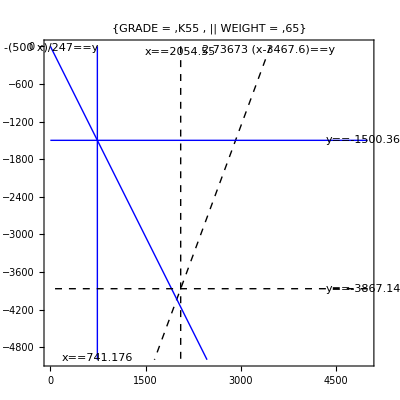

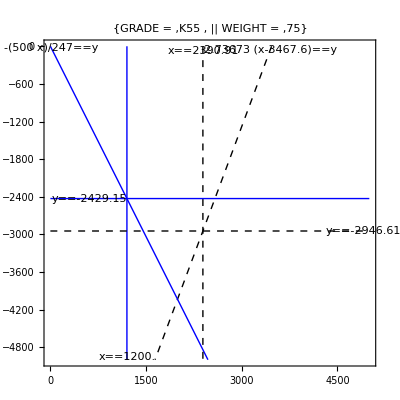

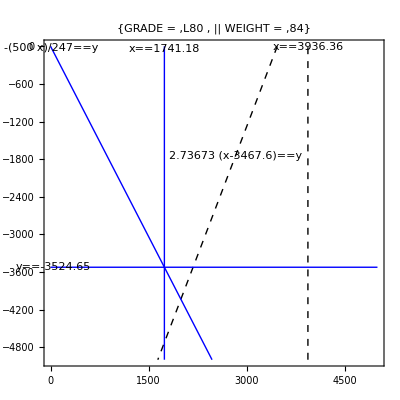

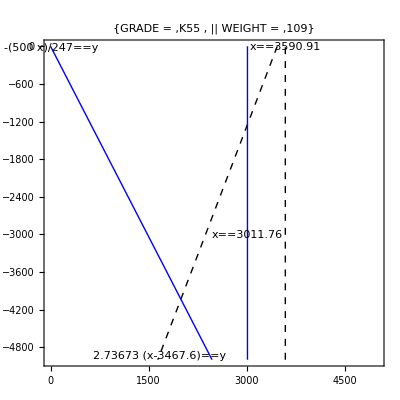

```mathematica
CaseLength=5000;
CaseOD=16;
plot=SelecPipe[BurstCoords,ColapseCoords,CaseOD,CaseLength];
plot[[1]]
plot[[2]]
plot[[3]]
plot[[4]]
```

```mathematica
Convert[2900 PSI, 1KilogramForce/Centimeter^2]
```

(203.89 KilogramForce)/Centimeter^2

```mathematica
(* 1 - Outside diameter(in) | 2 - Nominal weight(lb/ft) | 3 - Grade | 4 - Wall thickness (in) | 5 - Inside diameter (in) | 6 - Pipe collapse resistance (psi) | 7 - Body yield strength (1000 lbf) | 8 - Coupling type | 9 - Internal pressure resistance (psi) | 10 - Joint strength (1000 lbf) *)
```

```mathematica
ComputeSafetyFactors[BurstPressure_,ColapsePressute_,PipesTable_]:=Block[{i,BusrtSafetyFactor,ColapseSafetyFactor,BurstResistence,ColapseResistence,Grade,NominalWeight},


For[i=1,i≤Length[PipesTable],i++,

If[PipesTable[[i]][[1]]==16,


BurstResistence = PipesTable[[i]][[9]];
ColapseResistence = PipesTable[[i]][[6]];
Grade=PipesTable[[i]][[3]];
NominalWeight=PipesTable[[i]][[2]];
BusrtSafetyFactor=BurstResistence/BurstPressure//N;
ColapseSafetyFactor=ColapseResistence/ColapsePressute//N;
Print[" NominalWeight = ", NominalWeight, " || Grade = ",Grade , " || BusrtSafetyFactor = ",BusrtSafetyFactor, " || ColapseSafetyFactor = ",ColapseSafetyFactor];
];

];
];
```

```mathematica
BurstPressure=3467.6;
ColapsePressure=2470;
```

```mathematica
ComputeSafetyFactors[BurstPressure,ColapsePressure,PipesTable]
```

NominalWeight = 65 || Grade = K55 || BusrtSafetyFactor = 0.651748 || ColapseSafetyFactor = 0.255061

NominalWeight = 75 || Grade = K55 || BusrtSafetyFactor = 0.75845 || ColapseSafetyFactor = 0.412955

NominalWeight = 84 || Grade = L80 || BusrtSafetyFactor = 1.2487 || ColapseSafetyFactor = 0.59919

NominalWeight = 109 || Grade = K55 || BusrtSafetyFactor = 1.13912 || ColapseSafetyFactor = 1.03644